```mathematica
lst=Table[0,8,61];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
```

SetDelayed::shape: Lists {seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp} and {eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g→gg,h→7} are not the same shape.

General::munfl: 8.59599×10^-302 1.484×10^-16 is too small to represent as a normalized machine number; precision may be lost.

$Aborted

```mathematica
Rasterize[ListPlot[Import["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\corr_ana.dat","Table"],PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},Joined->True]]
```

-Graphics-

```mathematica
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\corr_ana.dat",lst]
corr0=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_0.dat",Number];
corr1=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_1.dat",Number];
corr2=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_2.dat",Number];
corr3=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_3.dat",Number];
corr4=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_4.dat",Number];
corr5=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_5.dat",Number];
corr6=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_6.dat",Number];
corr7=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_7.dat",Number];
```

F:\ThesisProject\RESULTS\26052023_corr_modified\corr_ana.dat

```mathematica
plst=Table[0,{i,8},{j,31},{k,2}];
For[i=0,i<8,i++,plst[[i+1]]=Transpose[{Table[i,{i,-30,30}],lst[[i+1]]}]];
```

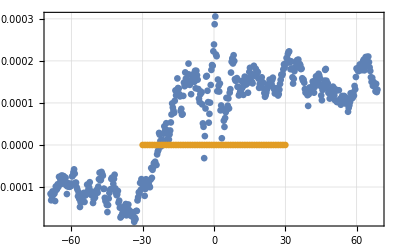

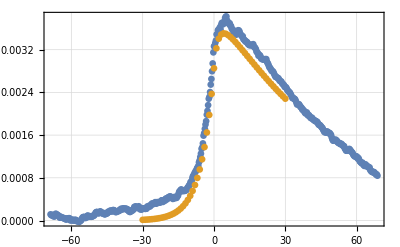

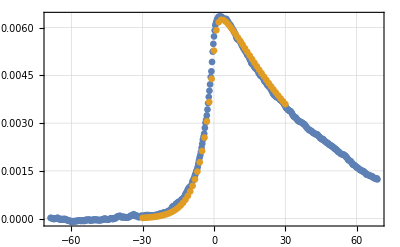

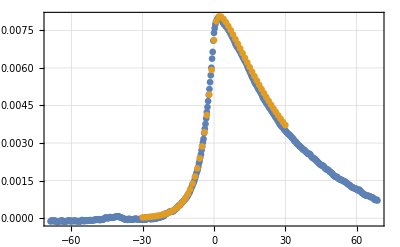

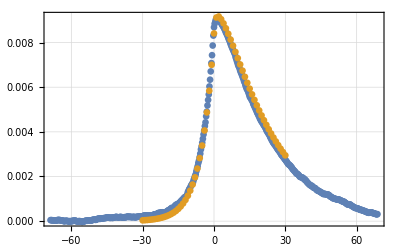

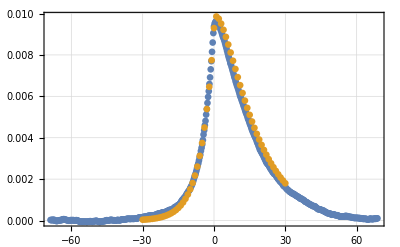

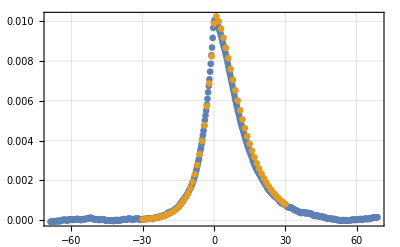

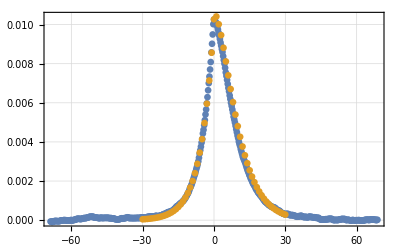

```mathematica
scalF=5.5;
pcr0=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr0}];

ListPlot[{pcr0,plst[[1]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr1=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr1}];

ListPlot[{pcr1,plst[[2]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr2=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr2}];

ListPlot[{pcr2,plst[[3]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr3=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr3}];

ListPlot[{pcr3,plst[[4]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr4=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr4}];

ListPlot[{pcr4,plst[[5]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr5=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr5}];

ListPlot[{pcr5,plst[[6]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr6=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr6}];

ListPlot[{pcr6,plst[[7]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr7=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr7}];

ListPlot[{pcr7,plst[[8]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
```

```mathematica
(**)
```

```mathematica
dlst=Table[0,8,31];
For[gg=0,gg<8,gg++,dlst[[gg+1]]=Table[lst[[gg+1,31-i]]-lst[[gg+1,31+i]],{i,-30,0}]];
```

```mathematica
Rasterize[ListPlot[dlst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,0},Joined->True]]
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\DCtau_eq.dat",dlst];
```

-Graphics-

```mathematica
(*24.05.2023*)
```

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

```mathematica
Rasterize[ListPlot[maxc,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},Joined->True]]
```

-Graphics-

```mathematica
Rasterize[ListPlot[maxt,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
(*25.05.2023*)
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat",lst]
```

F:\ThesisProject\RESULTS\25052023_extrema\h10.dat

```mathematica
ilst=Import["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat","Table"];
```

```mathematica
ilst[[1]]={0,Infinity};
```

```mathematica
fitMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,1]]}];
fitTMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,2]]}];
```

FittedModel[-0.0000219197+0.00102339 x-0.00016372 x^2+0.0000119369 x^3-3.28706×10^-7 x^4]

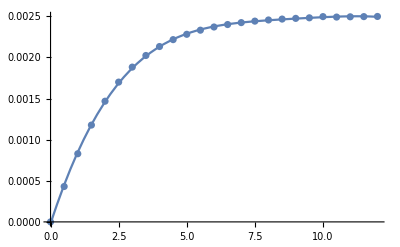

```mathematica
nlm=NonlinearModelFit[fitMax,a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
Show[ListPlot[ilst[[All,1]],DataRange->{0,12},PlotRange->All],Plot[nlm[x],{x,0,12}]]
```

FittedModel[18.7195-1.50103/x-4.71804 x+0.371601 x^2-0.00456264 x^3-0.000364738 x^4]

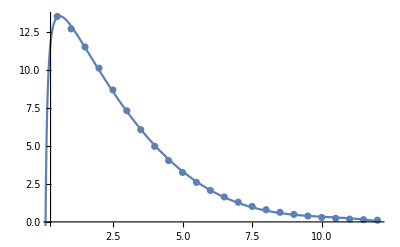

```mathematica
nlmt=NonlinearModelFit[fitTMax[[2;;25]],a+b x+c x^2+d x^3+e x^4+f x^(-1),{a,b,c,d,e,f},x]
Show[ListPlot[ilst[[All,2]],DataRange->{0,12},PlotRange->All],Plot[nlmt[x],{x,0,12}]]
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\fit.dat",{nlm//Normal,nlmt//Normal}]
```

F:\ThesisProject\RESULTS\25052023_extrema\fit.dat

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

(0 | 0.0562453 | 0.0887259 | 0.102058 | 0.107213 | 0.10916
0 | 0.0233935 | 0.0353066 | 0.0400117 | 0.0418152 | 0.0424933
0 | 0.00625079 | 0.0091827 | 0.0102691 | 0.0106702 | 0.0108184
0 | 0.0014678 | 0.00213307 | 0.0023707 | 0.00245623 | 0.00248632
0 | 0.000332398 | 0.000481201 | 0.000533496 | 0.000552089 | 0.000558832)

(0 | 0.269867 | 0.129315 | 0.052779 | 0.0202246 | 0.00755684
0 | 0.964786 | 0.476559 | 0.200015 | 0.0778965 | 0.0293205
0 | 3.3005 | 1.62697 | 0.679211 | 0.26338 | 0.0989795
0 | 10.101 | 4.96469 | 2.0674 | 0.800207 | 0.301444
0 | 28.5502 | 13.9992 | 5.81894 | 2.24996 | 0.843757)

{{38.3194,41.5955,43.0497,43.6496,43.9041},{15.9377,16.552,16.8776,17.0241,17.0908},{4.25861,4.30493,4.3317,4.34415,4.35119},{1.,1.,1.,1.,1.},{0.22646,0.225591,0.225038,0.224771,0.224763}}

FittedModel[-1.02185+44.2437/x]

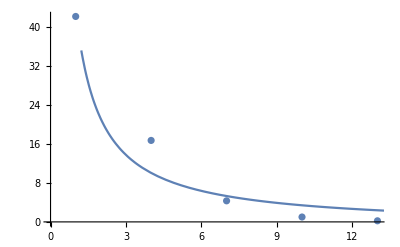

```mathematica
rate=Table[maxc[[i,2;;6]]/maxc[[4,2;;6]],{i,1,5}]
ratefit=Mean[Transpose[rate]];
ratefit=Transpose[{{1,4,7,10,13},ratefit}];
line=NonlinearModelFit[ratefit,a+b/x,{a,b,c,d},x]
Show[ListPlot[ratefit],Plot[line[x],{x,0,15}]]
```

{{0.0267168,0.0260469,0.0255292,0.0252742,0.0250688},{0.0955137,0.0959895,0.0967474,0.0973454,0.0972668},{0.326749,0.327708,0.328534,0.32914,0.328351},{1.,1.,1.,1.,1.},{2.82647,2.81974,2.81462,2.81173,2.79905}}

FittedModel[-0.0305447+0.0338354 ⅇ^(0.340939 x)]

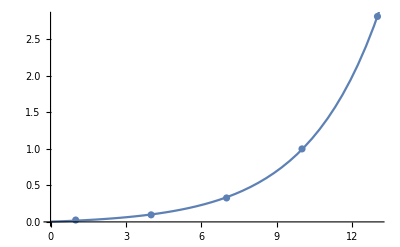

```mathematica
ratet=Table[maxt[[i,2;;6]]/maxt[[4,2;;6]],{i,1,5}]
ratetfit=Mean[Transpose[ratet]];
ratetfit=Transpose[{{1,4,7,10,13},ratetfit}];
linet=NonlinearModelFit[ratetfit,a+b Exp[c x],{a,b,c,d},x]
Show[ListPlot[ratetfit],Plot[linet[x],{x,0,15}]]
```

```mathematica
lmtM0=Limit[matJump,g->0]
eigVa0=Eigenvalues[lmtM0]
eigVeR0=Eigenvectors[lmtM0]
eigVeL0=Eigenvectors[Transpose[lmtM0]];
eigNVeL0=Table[eigVeL0[[i]]/(eigVeL0[[i]].eigVeR0[[i]]),{i,1,8}]
nessDist0=Limit[nessDist,g->0]
```

{{-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0,ⅇ^(h/4),0,0,0},{ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),0,0},{ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4),0,0,ⅇ^(-h/4),0},{0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4),0,0,0,ⅇ^(-3 h/4)},{ⅇ^(h/4),0,0,0,-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0},{0,ⅇ^(-h/4),0,0,ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4)},{0,0,ⅇ^(-h/4),0,ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4)},{0,0,0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4)}}

{0,-4 ⅇ^(-h/4),-2 ⅇ^(-h/4),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h-√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h+√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,1],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,2],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,3]}

{{ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1,ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1},6,{(ⅇ^(-3 h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[48 ⅇ^111+1+1+#1^3&,3]+12+3 ⅇ^h 1^4+Root[48 ⅇ^1+1+1+#1^3&,3]^5))/(2 (24 ⅇ^(3 h/2)+6 ⅇ^(h/2) Root[48 ⅇ^1+(1) #1+(1) 1+#1^3&,3]+3+ⅇ^1 1^2+ⅇ^h Root[48 ⅇ^1+1+1+#1^3&,3]^2)),1/(2 1),4,1,1}}
 |  |  |  |

{{1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2))},6,{(ⅇ^(-h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[1]+92 ⅇ^1 Root[1&,3]+10+1+3 ⅇ^h 1^4+Root[1&,3]^5))/(2 1 (1+(1)^2/(1)^2+1/1+1+(ⅇ^1 1)/(2 1^2)+(ⅇ^(-2 h) (1)^2)/(4 (1)^2))),6,1/1}}
 |  |  |  |

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
Limit[nessDist,g->Infinity]
```

{1/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),0,0,0,0,ⅇ^h/((1+ⅇ^(h/2))^2)}

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
xExp0=Dot[nessDist0,xL];
yExp0=Dot[nessDist0,yL];
{seigenVa,seigenVeL,nseigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigVa0,eigVeL0,eigNVeL0,eigVeR0,nessDist0,xExp0,yExp0};
```

```mathematica
lst[[3]]=Table[fCtauN[i]/.h->7,{i,-30,0}]~Join~Table[fCtauP[i]/.h->7,{i,1,30}];
```

General::munfl: 8.59599×10^-302 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.32866×10^-292 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Rasterize[ListPlot[{lst[[3]],lst[[1]],lst[[2]]},DataRange->{-30,30},PlotRange->All,Joined->True,AxesLabel->{"τ","C(τ)"},PlotLegends->Placed[{"γ→0","γ=10","γ→∞"},{0.8,0.8}]]]
```

-Graphics-

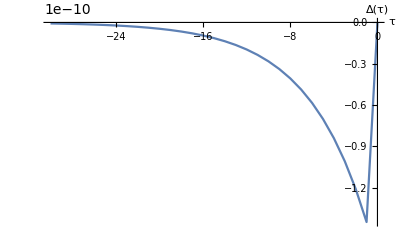

```mathematica
ListPlot[Table[lst[[31+i]]-lst[[31-i]],{i,30,0,-1}],DataRange->{-30,0},Joined->True,AxesLabel->{"τ","Δ(τ)"}]
```

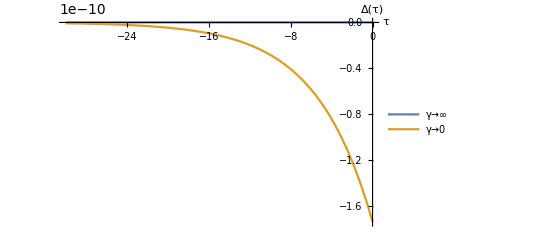

```mathematica
Plot[{fIDCtau[t]/.h->7,fDCtau[t]/.h->7},{t,-30,0},PlotRange->All,AxesLabel->{"τ","Δ(τ)"},PlotLegends->Placed[{"γ→∞","γ→0"},{0.1,0.8}]]
```

```mathematica
(*EQ degeneration*)
x1=1;
x2=1;
yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]))];
matJump=Transpose[({{-(fH[h,1]*3), fH[h,1], fH[h,1], 0, fH[h,1], 0, 0, 0}, {fH[h,2], -(fH[h,2]*3), 0, fH[h,2], 0, fH[h,2], 0, 0}, {fH[h,3], 0, -(fH[h,3]*3), fH[h,3], 0, 0, fH[h,3], 0}, {0, fH[h,4], fH[h,4], -(fH[h,4]*3), 0, 0, 0, fH[h,4]}, {fH[h,5], 0, 0, 0, -(fH[h,5]*3), fH[h,5], fH[h,5], 0}, {0, fH[h,6], 0, 0, fH[h,6], -(fH[h,6]*3), 0, fH[h,6]}, {0, 0, fH[h,7], 0, fH[h,7], 0, -(fH[h,7]*3), fH[h,7]}, {0, 0, 0, fH[h,8], 0, fH[h,8], fH[h,8], -(fH[h,8])}})];
eigenVa=Eigenvalues[matJump];
eigenVeR=Eigenvectors[matJump];
eigenVeL=Eigenvectors[Transpose[matJump]];
```

```mathematica
xL={1,2,3,4,1,2,3,4};
yL={1,1,1,1,2,2,2,2};
matA=-TensorProduct[yL,xL]+TensorProduct[xL,yL];
matPA=TensorProduct[xL,yL];
matNA=TensorProduct[yL,xL];
(* Find NESS distributions*)
fWTilde[ww_]:=Join[ww[[1;;Dimensions[ww][[1]]-1]],{Table[1,Dimensions[ww][[2]]]}];
nessDist=Dot[Inverse[fWTilde[matJump]],Transpose[Table[0,Dimensions[fWTilde[matJump]][[2]]-1]~Join~{1}]];
xExp=xL.nessDist;
yExp=yL.nessDist;
fDCtau[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matA]],{i,8}])/(sxExp*syExp)];
fCtauP[t_]:=
N[(Sum[Exp[seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matPA]],{i,8}])/(sxExp*syExp)-1];
fCtauN[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matNA]],{i,8}])/(sxExp*syExp)-1];
```

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.h->7;
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
Rasterize[Plot[fDCtau[t],{t,-30,0},AxesLabel->{"τ","Δ(τ)"}]]
```

-Graphics-

```mathematica
lst=Table[fDCtau[i],{i,-30,0,0.5}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}